```mathematica
estimation of Re and R/Subscript[R, 1]
```

```mathematica
ρ=1.27;v=0.001;Subscript[R, 1]=0.015;R=0.0001;μ=1.7*10^-5;u=Subscript[R, 1]^2/R^2 v;Subscript[L, 0]=2R;
ρ u Subscript[L, 0]/μ
```

336.176

```mathematica
R=0.00025;Subscript[R, 1]=0.01;L=5;μ=1.7*10^-5;v=6*10^-3;
(8π v Subscript[R, 1]^4 L μ)/R^4
Clear["Global`*",Subscript]
```

32.8133

```mathematica
air viscosity measurement
```

```mathematica
DSolve[{D[m[x], x]== a(b-c m[x])^d,m[l]==A},m[x],x]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m[x]→(b-((b-A c)^(1-d)-a c (-1+d) (l-x))^(1/(1-d)))/c}}

```mathematica
DSolve[{D[m[x], x]== a(b-c m[x])^d,m[l]==0},m[x],x]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m[x]→(b-(b^(1-d)-a c (-1+d) (l-x))^(1/(1-d)))/c}}

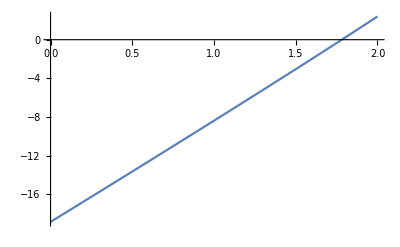

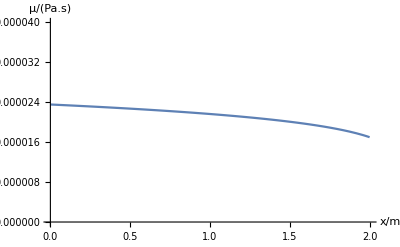

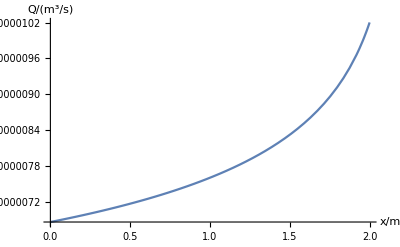

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{2.}

```mathematica
k=1.41;Subscript[p, 0]=10^5;F=15.72;R=.0001;Subscript[R, 1]=.00725;v=.00618;l=2;Subscript[μ, 0]=1.7*10^-5;
a=Subscript[μ, 0]^((2k-3)/(2k-2));b=1+F/(π Subscript[R, 1]^2 Subscript[p, 0]);c=(8 Subscript[R, 1]^2 v)/(R^4 Subscript[p, 0] Subscript[μ, 0]^(1/(2(1-k))));d=1/2-3/(4 k);
M[x_]:=(b-(1-a c (-1+d) (l-x))^(1/(1-d)))/c;
μ[x_]:=Evaluate@(D[M[x],x]^((2k-2)/(2k-3)));
Plot[M[x],{x,0,l}]
Plot[μ[x],{x,0,l},PlotRange->{0,0.00004},AxesLabel->{"x/m","μ/(Pa.s)"}]
Plot[π Subscript[R, 1]^2 v(μ[x]/Subscript[μ, 0])^(1/(2(1-k))),{x,0,l},AxesLabel->{"x/m","Q/(m^3/s)"}]
x/.Solve[μ[x]==Subscript[μ, 0],x]//FullSimplify
```

```mathematica
a=Subscript[μ, 0]^((2k-3)/(2k-2));b=1+F/(π Subscript[R, 1]^2 Subscript[p, 0]);c=(8 Subscript[R, 1]^2 v)/(R^4 Subscript[p, 0] Subscript[μ, 0]^(1/(2(1-k))));d=1/2-3/(4 k);
M[x_]:=(b-(1-a c (-1+d) (l-x))^(1/(1-d)))/c;
Solve[M[0]==0,Subscript[μ, 0]]//FullSimplify
```

```mathematica
{{Subscript[μ, 0]->(k R^4 Subscript[p, 0] (-1+(1+F/(π Subscript[p, 0] Subscript[R, 1]^2))^(1/2+3/(4 k))))/(2 (3+2 k) l v Subscript[R, 1]^2)}}
```

```mathematica
Μ=A+B(C+D L)^((2 k)/(1+k))    A=(π R^4 Subscript[p, 0])/(8 Q)+(F R^4)/(8 Q Subscript[R, 1]^2),B=-(R^4 Subscript[p, 0])/(8Q),C=4 ((4^(-(2 k)/(1+k)) (F+π Subscript[p, 0] Subscript[R, 1]^2))/(Subscript[p, 0] Subscript[R, 1]^2))^((1+k)/(2 k)),D=-(4 (1+k) L π^(1/2 (-1+1/k)) Q Subscript[μ, 0])/(k R^4 Subscript[p, 0])
```

```mathematica
k=1.41;Subscript[p, 0]=1.01*10^5;Subscript[ρ, 0]=1.27;μ=1.7*10^-5;
NDSolve[{D[ρ[r,x,t], t]+v[r,x,t]D[ρ[r,x,t], x]+ρ[r,x,t]D[v[r,x,t], x]==0,D[v[r,x,t], t]+v[r,x,t]D[v[r,x,t], x]==-(Subscript[p, 0] k ρ[r,x,t]^(k-2))/Subscript[ρ, 0]^k D[ρ[r,x,t], x]+μ/ρ[r,x,t](1/r(D[v[r,x,t], r]+D[D[v[r,x,t], r], r])+D[D[v[r,x,t], x], x])},{v[r,x,t],ρ[r,x,t]},{r,0,5},{x,0,5},{t,0,10}]
```

```mathematica
Clear["Global`*",Subscript]
```

```mathematica
evaluating tube deformation
```

```mathematica
DSolve[{ϵr[r,φ]==D[ur[r,φ], r],ϵφ[r,φ]==ur[r,φ]/r,ϵr[r,φ]==(σr[r,φ]-ν σφ[r,φ])/e,ϵφ[r,φ]==(σφ[r,φ]-ν σr[r,φ])/e,D[σr[r,φ], r]+(σr[r,φ]-σφ[r,φ])/r==0},{ur,ϵr,ϵφ,σr,σφ},{r,φ}]
```

```mathematica
DSolve[{ϵr[r,φ]==D[ur[r,φ], r],ϵφ[r,φ]==ur[r,φ]/r,ϵr[r,φ]==(σr[r,φ]-Subscript[ν, rφ] σφ[r,φ])/Subscript[e, r],ϵφ[r,φ]==(σφ[r,φ]-Subscript[ν, φr] σr[r,φ])/Subscript[e, φ],D[σr[r,φ], r]+(σr[r,φ]-σφ[r,φ])/r==0},{ur,ϵr,ϵφ,σr,σφ},{r,φ}]
```

```mathematica
DSolve[{D[(e D[ur[r,φ], r]+ ν/(1-ν^2)((e ur[r,φ])/r+ν e D[ur[r,φ], r])), r]+(e D[ur[r,φ], r]+(ν-1)/(1-ν^2)((e ur[r,φ])/r+ν e D[ur[r,φ], r]))/r==0},ur,{r,φ}]
```

{{ur→Function[{r,φ},(C[1][φ])/r+r C[2][φ]]}}

```mathematica
DSolve[{1/(1-ν1 ν2)D[(e1 D[ur[r,φ], r]+ν1 (e2 ur[r,φ])/r), r]+(1/(1-ν1 ν2)(e1 D[ur[r,φ], r]+ν1 (e2 ur[r,φ])/r)-((e2 ur[r,φ])/r+ν2/(1-ν1 ν2)(e1 D[ur[r,φ], r]+ν1 (e2 ur[r,φ])/r)))/r==0},{ur},{r,φ}]
```

{{ur→Function[{r,φ},r^((ⅈ √e2 (-(ⅈ (-e2 ν1+e1 ν2))/(√e1 √e2)-√(-4-(-e2 ν1+e1 ν2)^2/(e1 e2))))/(2 √e1)) C[1][φ]+r^((ⅈ √e2 (-(ⅈ (-e2 ν1+e1 ν2))/(√e1 √e2)+√(-4-(-e2 ν1+e1 ν2)^2/(e1 e2))))/(2 √e1)) C[2][φ]]}}

```mathematica
Clear["Global`*",Subscript]
ur[r_,φ_]:=C[1]/r+r C[2];
ϵr[r_,φ_]:=D[ur[r,φ], r];
ϵφ[r_,φ_]:=ur[r,φ]/r;
Solve[{Evaluate[(e (ϵr[R,φ]+ϵφ[R,φ] ν))/(-1+ν^2)]==F/Subscript[S, 1],Evaluate[-(e (ϵr[Subscript[R, 2],φ]+ϵφ[Subscript[R, 2],φ] ν))/(-1+ν^2)]==0},{C[1],C[2]}]//FullSimplify
```

{{C[1]→-(F R^2 (1+ν) R_2^2)/(e (R^2-R_2^2) S_1),C[2]→(F R^2 (-1+ν))/(e (R^2-R_2^2) S_1)}}

5.28081×10^-6

1.33426×10^-6

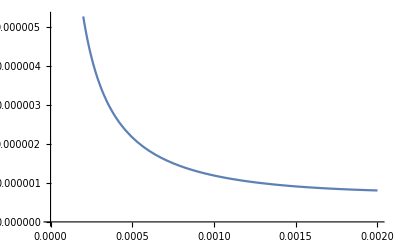

```mathematica
F=100;Subscript[S, 1]=0.0005;L=10;v=0.001;R=0.0002;Subscript[R, 2]=0.002;ν=0.3;e=10^7;
Subscript[u, R]=(-F R^2 (1+ν) Subscript[R, 2]^2)/(e (R^2-Subscript[R, 2]^2) Subscript[S, 1])1/R+(F R^2 (-1+ν))/(e (R^2-Subscript[R, 2]^2) Subscript[S, 1])R
Subscript[ϵ, μ]=((4F)/(Subscript[S, 1] L)(π R^3)/(8v Subscript[S, 1]))^2 Re@Subscript[u, R]
Plot[(-F R^2 (1+ν) Subscript[R, 2]^2)/(e (R^2-Subscript[R, 2]^2) Subscript[S, 1])1/r+(F R^2 (-1+ν))/(e (R^2-Subscript[R, 2]^2) Subscript[S, 1])r,{r,R,Subscript[R, 2]},PlotRange->{0,Subscript[u, R]}]
```

```mathematica
Clear["Global`*",Subscript]
b=(e1 ν2-e2 ν1)/(2 e1);
c=(√(4e1 e2+(e1 ν2-e2 ν1)^2))/(2 e1);
ur[r_,φ_]:=Subscript[a, 1] r^(b+c)+Subscript[a, 2] r^(b-c);
ϵr[r_,φ_]:=D[ur[r,φ], r];
ϵφ[r_,φ_]:=ur[r,φ]/r;
Solve[{Evaluate[(e1 ϵr[R,φ]+e2 ϵφ[R,φ] ν1)/(-1+ν1 ν2)]==F/Subscript[S, 1],Evaluate[-(e2 ϵφ[Subscript[R, 2],φ]+e1 ϵr[Subscript[R, 2],φ] ν2)/(-1+ν1 ν2)]==0},{Subscript[a, 1],Subscript[a, 2]}]//FullSimplify
```

```mathematica
DSolve[{(Subscript[R, 0]+p[x](Subscript[A, 1] Subscript[R, 0]^(b+c)+Subscript[A, 2] Subscript[R, 0]^(b-c)))^4 D[p[x],x]==-8 Subscript[R, 1]^2 v μ,p[0]==F/Subscript[S, 1],p[L]==0},{p[x]},x]
```

{}

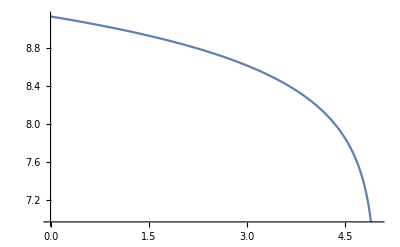

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;v=0.001;F=30;
μ=0.001;Subscript[S, 1]=π Subscript[R, 1]^2;Subscript[a, 9]=1.56146*^-6;Subscript[b, 9]=-6.97062*^-6;Subscript[c, 9]=0.00001859;Subscript[d, 9]=0.000038;
NDSolve[{(Subscript[R, 0]+Subscript[a, 9] p[x]^4+Subscript[b, 9] p[x]^3+Subscript[c, 9] p[x]^2+Subscript[d, 9] p[x])^4 D[p[x],x]==-8 Subscript[R, 1]^2 v μ,p[L]==0},{p[x]},{x,0,L}];
Plot[p[x]/.%,{x,0,L}]
```

```mathematica
Clear["Global`*",Subscript]
Subscript[P, 0]=Subscript[F, lami]/(π Subscript[R, 1]^2);Subscript[a, 9]=1.56146*^-6;Subscript[b, 9]=-6.97062*^-6;Subscript[c, 9]=0.00001859;Subscript[d, 9]=0.000038;
p=Evaluate[p/.Solve[a p^4+b p^3+c p^2+d p==Subscript[U, Subscript[R, 0]],p][[2]]];
1/(8L μ Subscript[R, 1]^2)(Subscript[F, lami]/(π Subscript[R, 1]^2)(Subscript[R, 0]+a Subscript[P, 0]^4+b Subscript[P, 0]^3+c Subscript[P, 0]^2+d Subscript[P, 0])^4- 4∫_0^(a Subscript[P, 0]^4+b Subscript[P, 0]^3+c Subscript[P, 0]^2+d Subscript[P, 0]) p Subscript[U, Subscript[R, 0]]^3 ⅆ Subscript[U, Subscript[R, 0]])//FullSimplify
```

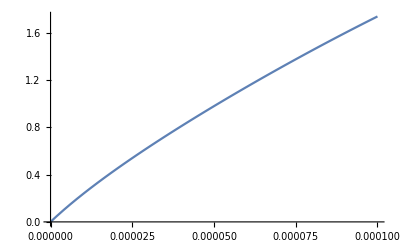

```mathematica
Plot[P/.Solve[Subscript[a, 9] P^4+Subscript[b, 9] P^3+Subscript[c, 9] P^2+Subscript[d, 9] P==U,P][[2]],{U,0,0.0001}]
```

```mathematica
Clear["Global`*",Subscript]
Subscript[P, 0]=Subscript[F, lami]/(π Subscript[R, 1]^2);
p=Evaluate[p/.Solve[a p^4+b p^3+c p^2+d p==Subscript[U, Subscript[R, 0]],p][[2]]];
Solve[L μ==1/(8v Subscript[R, 1]^2)(Subscript[F, lami]/(π Subscript[R, 1]^2)(Subscript[R, 0]+a Subscript[P, 0]^4+b Subscript[P, 0]^3+c Subscript[P, 0]^2+d Subscript[P, 0])^4- 4∫_0^(a Subscript[P, 0]^4+b Subscript[P, 0]^3+c Subscript[P, 0]^2+d Subscript[P, 0]) p Subscript[U, Subscript[R, 0]]^3 ⅆ Subscript[U, Subscript[R, 0]]) ,Subscript[F, lami]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[L μ==1/(8 v R_1^2)(-4 ∫_0^((a F_lami^4)/(π^4 R_1^8)+(b F_lami^3)/(π^3 R_1^6)+(c F_lami^2)/(π^2 R_1^4)+(d F_lami)/(π R_1^2)) U_R_0^3 (-b/(4 a)-1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d-12 a U_R_0))/(3 a (2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0+√(-4 (c^2-3 b d-12 a U_R_0)^3+(2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0+√(-4 (c^2-3 b d-12 a U_R_0)^3+(2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0)^2))^(1/3))/(3 2^(1/3) a))+1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d-12 a U_R_0))/(3 a (2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0+√(-4 (c^2-3 b d-12 a U_R_0)^3+(2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0+√(-4 (c^2-3 b d-12 a U_R_0)^3+(2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0)^2))^(1/3))/(3 2^(1/3) a)-(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d-12 a U_R_0))/(3 a (2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0+√(-4 (c^2-3 b d-12 a U_R_0)^3+(2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0+√(-4 (c^2-3 b d-12 a U_R_0)^3+(2 c^3-9 b c d+27 a d^2-27 b^2 U_R_0+72 a c U_R_0)^2))^(1/3))/(3 2^(1/3) a)))))ⅆ U_R_0+(F_lami (R_0+(a F_lami^4)/(π^4 R_1^8)+(b F_lami^3)/(π^3 R_1^6)+(c F_lami^2)/(π^2 R_1^4)+(d F_lami)/(π R_1^2))^4)/(π R_1^2)),F_lami]

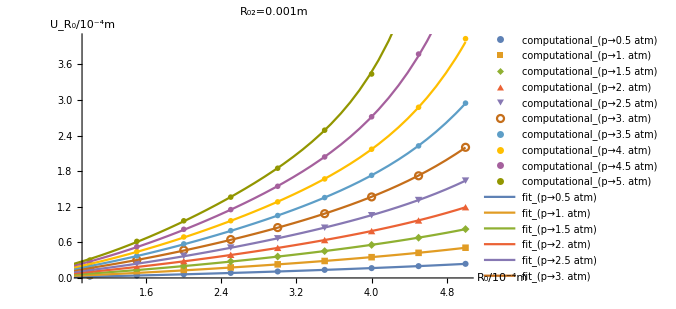

{(R^2)_1→0.999732,(R^2)_2→0.999772,(R^2)_3→0.999781,(R^2)_4→0.999835,(R^2)_5→0.999886,(R^2)_6→0.999878,(R^2)_7→0.999929,(R^2)_8→0.999918,(R^2)_9→0.999875,(R^2)_10→0.999832}

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=Table[1+0.5i,{i,0,8}];
Subscript[Subscript[U, R], out1mm]=10^4Transpose@Take[(Import@"C:\\Users\\Numerical_Lab3\\Documents\\大学物理实验3\\粘滞系数\\nonlinear defomation of silica gel.xlsx")[[1]],{5,13},{4,-3}];
p=Join[Table[Table[5*10^4i,{i,1,10}],{j,1,6}],{Table[5*10^4i,{i,1,9}]},{Table[5*10^4i,{i,1,8}]},{Table[5*10^4i,{i,1,7}]}];
n=Length@Subscript[Subscript[U, R], out1mm];
n2=Length@Subscript[Subscript[U, R], out1mm][[1]];
Table[Subscript[len, i]=Length@(Transpose@PadRight[p,{n2,n},null]/.null->Sequence[])[[i]],{i,1,n}];
Table[Subscript[sol, i]=NMinimize[Total@Table[(Subscript[Subscript[U, R], out1mm][[i]][[j]]- Subscript[a, i](Subscript[R, 0][[j]])^(Subscript[b, i]+Subscript[c, i])-Subscript[d, i](Subscript[R, 0][[j]])^(Subscript[b, i]-Subscript[c, i]))^2,{j,1,Subscript[len, i]}],{Subscript[a, i],Subscript[b, i],Subscript[c, i],Subscript[d, i]},Method->"RandomSearch"],{i,1,n}];
Evaluate@Table[Subscript[a, i],{i,1,n}]=Table[Subscript[a, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[b, i],{i,1,n}]=Table[Subscript[b, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[c, i],{i,1,n}]=Table[Subscript[c, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[d, i],{i,1,n}]=Table[Subscript[d, i]/.Subscript[sol, i][[2]],{i,1,n}];
Show[ListPlot[Table[Transpose@{Subscript[R, 0],Subscript[Subscript[U, R], out1mm][[i]]},{i,1,n}],ImageSize->500,PlotMarkers->Automatic,AxesLabel->{Style["R_0/10^-4m",Medium],Style["U_R_0/10^-4m",Medium]},PlotLabel->"R_0_2=0.001m",PlotRange->All,PlotLegends->LineLegend[Table[Subscript[computational, "p"->0.5i atm],{i,1,n}],LegendFunction->"Frame"]],
Plot[Evaluate@Table[Subscript[a, i] r^(Subscript[b, i]+Subscript[c, i])+Subscript[d, i] r^(Subscript[b, i]-Subscript[c, i]),{i,1,n}],{r,0,5},PlotRange->{0,4.5},PlotLegends->LineLegend[Table[Subscript[fit, "p"->0.5i atm],{i,1,n}],LegendFunction->"Frame"],PlotStyle->Automatic,ImageSize->600]] 
Table[Subscript["R^2", i]-> 1-Sum[(Subscript[Subscript[U, R], out1mm][[i]][[j]]-Subscript[a, i](Subscript[R, 0][[j]])^(Subscript[b, i]+Subscript[c, i])-Subscript[d, i](Subscript[R, 0][[j]])^(Subscript[b, i]-Subscript[c, i]))^2,{j,1,Subscript[len, i]}]/Sum[(Subscript[Subscript[U, R], out1mm][[i]][[j]]-Sum[Subscript[Subscript[U, R], out1mm][[i]][[j]],{j,1,Subscript[len, i]}]/Subscript[len, i])^2,{j,1,Subscript[len, i]}],{i,1,n}]
```

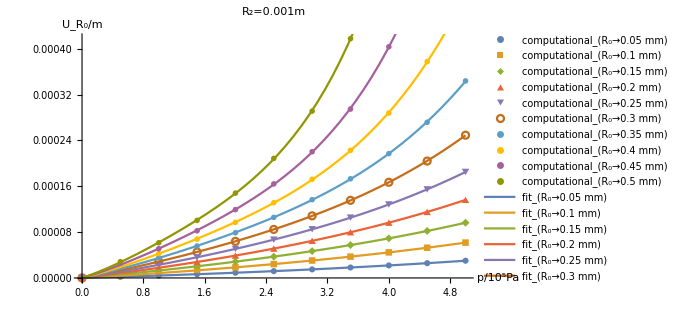

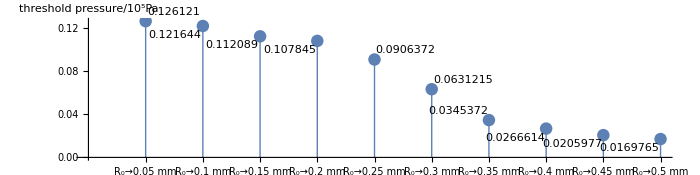

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=Table[0.0001+0.00005i,{i,0,8}];
Subscript[Subscript[U, R], out1mm]=Take[(Import@"C:\\Users\\Numerical_Lab3\\Documents\\大学物理实验3\\粘滞系数\\nonlinear defomation of silica gel.xlsx")[[1]],{5,14},{3,-3}];
p=Join[Table[Table[.5i,{i,0,10}],{j,1,7}],{Table[.5i,{i,0,9}]},{Table[.5i,{i,0,8}]},{Table[.5i,{i,0,7}]}];
n=Length@Subscript[Subscript[U, R], out1mm];
n2=Length@Subscript[Subscript[U, R], out1mm][[1]];
Table[Subscript[sol, i]=NMinimize[Total@Table[(Subscript[Subscript[U, R], out1mm][[i]][[j]]-Subscript[a, i](p[[i]][[j]])^4-Subscript[b, i](p[[i]][[j]])^3-Subscript[c, i](p[[i]][[j]])^2-Subscript[d, i] p[[i]][[j]])^2,{j,1,Length@(PadRight[p,{n,n2},null]/.null->Sequence[])[[i]]}],{Subscript[a, i],Subscript[b, i],Subscript[c, i],Subscript[d, i]},Method->"RandomSearch"],{i,1,n}];
Evaluate@Table[Subscript[a, i],{i,1,n}]=Table[Subscript[a, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[b, i],{i,1,n}]=Table[Subscript[b, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[c, i],{i,1,n}]=Table[Subscript[c, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[d, i],{i,1,n}]=Table[Subscript[d, i]/.Subscript[sol, i][[2]],{i,1,n}];
Show[ListPlot[Table[Transpose@{p[[i]],Take[Subscript[Subscript[U, R], out1mm][[i]],{1,Length@(PadRight[p,{n,n2},null]/.null->Sequence[])[[i]]}]},{i,1,n}],ImageSize->500,PlotMarkers->Automatic,AxesLabel->{Style["p/10^5Pa",Medium],Style["U_R_0/m",Medium]},PlotLabel->"R_2=0.001m",PlotRange->All,PlotLegends->LineLegend[Table[Subscript[computational, "R_0"->0.05i mm],{i,1,n}],LegendFunction->"Frame"]],Plot[Evaluate@Table[Subscript[a, i] P^4+Subscript[b, i] P^3+Subscript[c, i] P^2+Subscript[d, i] P,{i,1,n}],{P,0,5},PlotLegends->LineLegend[Table[Subscript[fit, "R_0"->0.05i mm],{i,1,n}],LegendFunction->"Frame"],PlotRange->{0,0.00044},PlotStyle->Automatic,ImageSize->700]] 
ListPlot[Labeled[#,#]&/@(Flatten@Table[P/.Solve[Subscript[a, i] P^4+Subscript[b, i] P^3+Subscript[c, i] P^2==0.01 Subscript[d, i] P,P,Reals][[2]],{i,1,n}]),Filling->Bottom,AxesLabel->{,"threshold pressure/10^5Pa"},FillingStyle->{Blue,Thick},Ticks->{Transpose@{Table[i,{i,1,n}],Table["R_0"->0.05i mm,{i,1,n}]},Automatic},TicksStyle->Directive["Label", 8.2],ImageSize->700,AspectRatio->0.25]
```

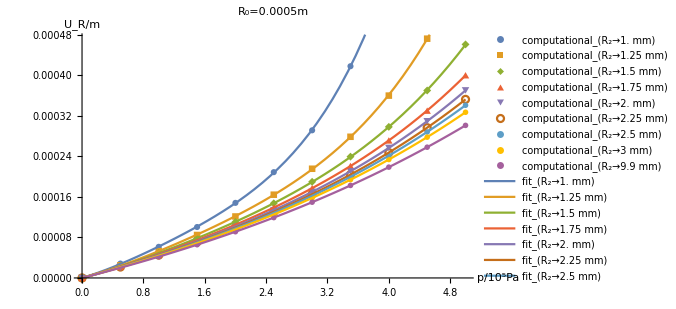

```mathematica
Clear["Global`*",Subscript]
R2=Table[0.001+0.00025i,{i,0,6}];
Subscript[Subscript[U, R], in0.5mm]=Take[(Import@"C:\\Users\\Numerical_Lab3\\Documents\\大学物理实验3\\粘滞系数\\nonlinear defomation of silica gel.xlsx")[[1]],{19,27},{3,-3}];
p=Join[{Table[.5i,{i,0,7}]},{Table[.5i,{i,0,9}]},Table[Table[.5i,{i,0,10}],{j,1,7}]];
n=Length@Subscript[Subscript[U, R], in0.5mm];
n2=Length@Subscript[Subscript[U, R], in0.5mm][[1]];
Table[Subscript[sol, i]=NMinimize[Total@Table[(Subscript[Subscript[U, R], in0.5mm][[i]][[j]]-Subscript[a, i](p[[i]][[j]])^4-Subscript[b, i](p[[i]][[j]])^3-Subscript[c, i](p[[i]][[j]])^2-Subscript[d, i] p[[i]][[j]])^2,{j,1,Length@(PadRight[p,{n,n2},null]/.null->Sequence[])[[i]]}],{Subscript[a, i],Subscript[b, i],Subscript[c, i],Subscript[d, i]},Method->"RandomSearch"],{i,1,n}];
Evaluate@Table[Subscript[a, i],{i,1,n}]=Table[Subscript[a, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[b, i],{i,1,n}]=Table[Subscript[b, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[c, i],{i,1,n}]=Table[Subscript[c, i]/.Subscript[sol, i][[2]],{i,1,n}];
Evaluate@Table[Subscript[d, i],{i,1,n}]=Table[Subscript[d, i]/.Subscript[sol, i][[2]],{i,1,n}];
Show[ListPlot[Table[Transpose@{p[[i]],Take[Subscript[Subscript[U, R], in0.5mm][[i]],{1,Length@(PadRight[p,{n,n2},null]/.null->Sequence[])[[i]]}]},{i,1,n}],ImageSize->500,PlotMarkers->Automatic,PlotLabel->"R_0=0.0005m",AxesLabel->{Style["p/10^5Pa",Medium],Style["U_R/m",Medium]},PlotRange->All,PlotLegends->LineLegend[Flatten@{Table[Subscript[computational, "R_2"->(1+0.25i)mm],{i,0,n-3}],Subscript[computational, "R_2"->3mm],Subscript[computational, "R_2"->9.9mm]},LegendFunction->"Frame"]],Plot[Evaluate@Table[Subscript[a, i] P^4+Subscript[b, i] P^3+Subscript[c, i] P^2+Subscript[d, i] P,{i,1,n}],{P,0,5},PlotLegends->LineLegend[Flatten@{Table[Subscript[fit, "R_2"->(1+0.25i)mm],{i,0,n-3}],Subscript[fit, "R_2"->3mm],Subscript[fit, "R_2"->9.9mm]},LegendFunction->"Frame"],PlotRange->{0,0.00048},PlotStyle->Automatic,ImageSize->700]]
```

```mathematica
Subscript[R, 0]^4/(8 L π μ Subscript[R, 1]^4)Subscript[F, lami]+(Subscript[C, 1] Subscript[R, 0]^3)/(2 L π^2 μ Subscript[R, 1]^6)Subscript[F, lami]^2+(3 Subscript[C, 1]^2 Subscript[R, 0]^2)/(4 L π^3 μ Subscript[R, 1]^8)Subscript[F, lami]^3+(Subscript[C, 1]^3 Subscript[R, 0])/(2 L π^4 μ Subscript[R, 1]^10)Subscript[F, lami]^4+Subscript[C, 1]^4/(40 L π^5 μ Subscript[R, 1]^12)Subscript[F, lami]^5
∑_(i=0)^4 (k Subscript[p, 0] Subscript[R, 0]^(4-i)Subscript[C, 1]^i((1+F^(i+1)/(π Subscript[p, 0] Subscript[R, 1]^(i+1)))^(1/2+3/(4 k))-1))/(2 (3+2 k) L v Subscript[R, 1]^(i+1))
```

```mathematica
processing experimental data
```

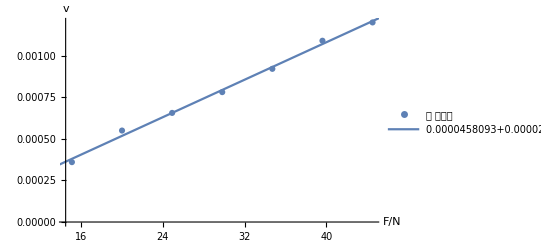

μ_H2O→0.00176553 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[1.542+0.5i,{i,0,6}];
Subscript[v, H2O]={0.00036,0.00055,0.000656,0.000781,0.000921,0.00109,0.0012};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

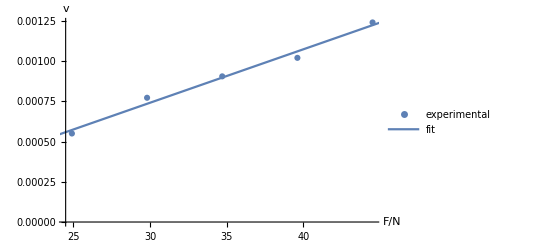

μ_H2O→0.00149697 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[1.542+0.5i,{i,2,6}];
Subscript[v, H2O]={0.00055,0.000772,0.000905,0.00102,0.00124};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

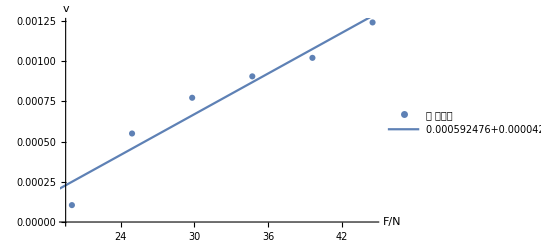

μ_H2O→0.00118173 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[1.542+0.5i,{i,1,6}];
Subscript[v, H2O]={0.000105,0.00055,0.000772,0.000905,0.00102,0.00124};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

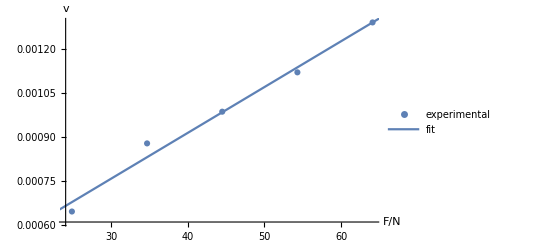

μ_H2O→0.0031857 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[0.542+i,{i,2,6}];
Subscript[v, H2O]={0.000646,0.000878,0.000986,0.00112,0.00129};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

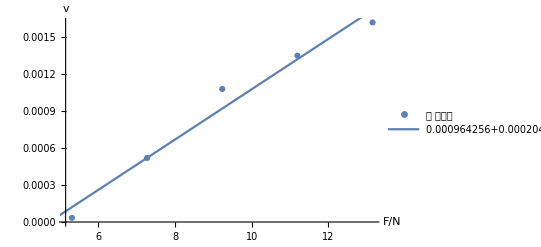

μ_H2O→0.000769808 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={3.39*10^-5,5.20*10^-4,0.00108,0.00135,0.00162};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

```mathematica
Subscript[d, 9]
```

0.0000380004

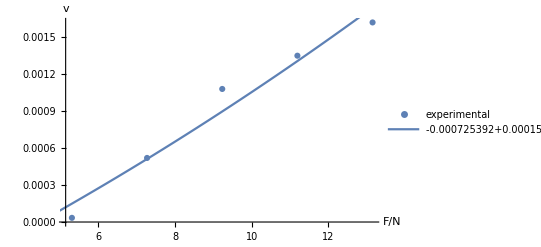

μ_H2O→0.00104506 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={3.39*10^-5,5.20*10^-4,0.00108,0.00135,0.00162};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 ("F")^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 ("F")^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 ("F")^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 ("F")^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 "F")+b//Simplify},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

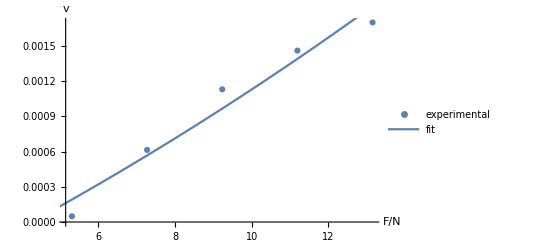

μ_H2O→0.00100891 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={4.89*10^-05,6.14*10^-04,0.00113,0.00146,0.0017};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

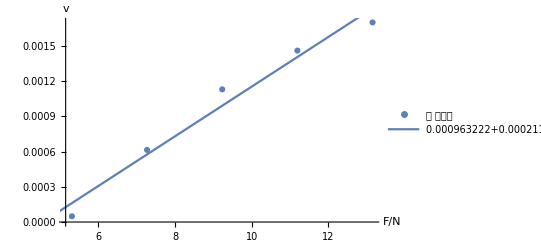

μ_H2O→0.000742714 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={4.89*10^-05,6.14*10^-04,0.00113,0.00146,0.0017};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

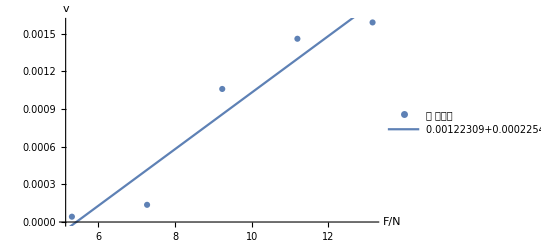

μ_H2O→0.000697326 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={4.24*10^-05,1.37*10^-04,0.00106,0.00146,0.00159};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

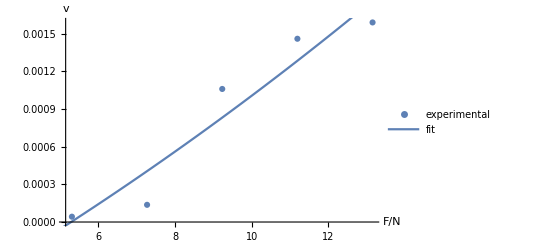

μ_H2O→0.000944548 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={4.24*10^-05,1.37*10^-04,0.00106,0.00146,0.00159};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

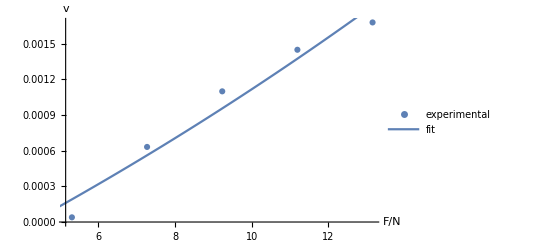

μ_H2O→0.00102114 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={3.95*10^-05,6.32*10^-04,0.0011,0.00145,0.00168};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

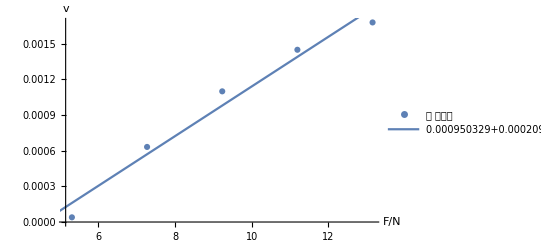

μ_H2O→0.000751629 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={3.95*10^-05,6.32*10^-04,0.0011,0.00145,0.00168};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

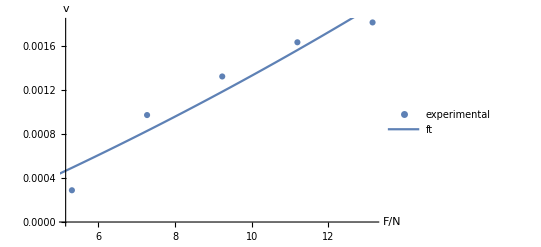

μ_H2O→0.00113259 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={2.88*10^-04,9.70*10^-04,0.00132,0.00163,0.00181};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{ft},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

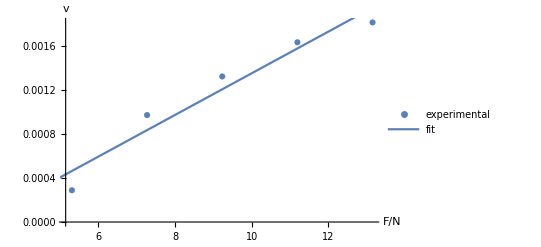

μ_H2O→0.000831783 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={2.88*10^-04,9.70*10^-04,0.00132,0.00163,0.00181};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

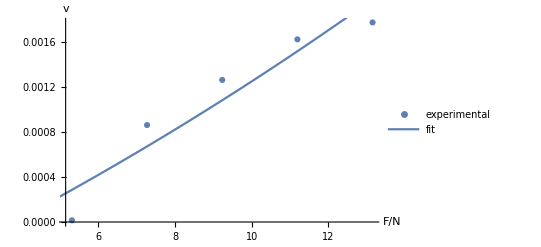

μ_H2O→0.000983891 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={1.47*10^-05,8.60*10^-04,0.00126,0.00162,0.00177};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

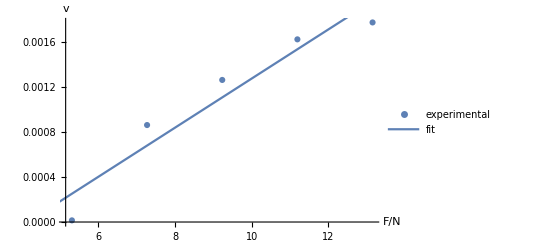

μ_H2O→0.000721427 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={1.47*10^-05,8.60*10^-04,0.00126,0.00162,0.00177};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

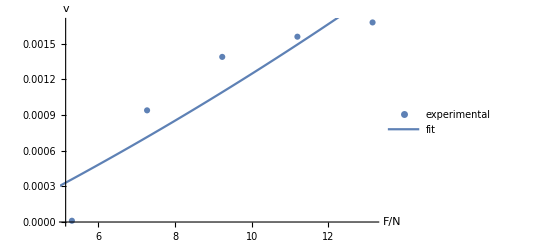

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={1.07*10^-05,9.40*10^-04,0.00139,0.00156,0.00168};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

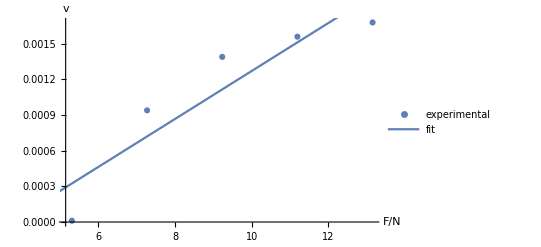

μ_H2O→0.000778287 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={1.07*10^-05,9.40*10^-04,0.00139,0.00156,0.00168};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

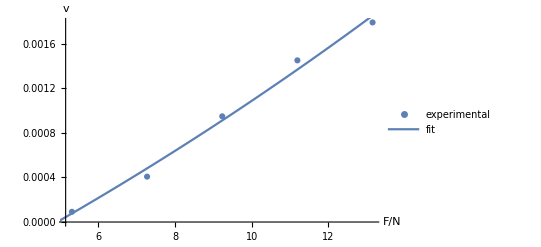

μ_H2O→0.000936967 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.0000916,0.000407,0.000948,0.00145,0.00179};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

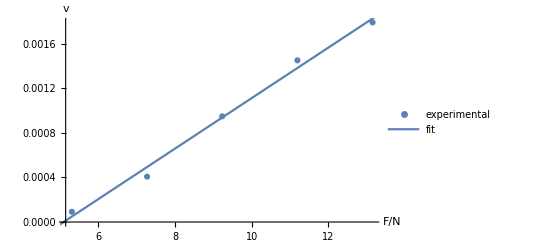

μ_H2O→0.000693933 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.0000916,0.000407,0.000948,0.00145,0.00179};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

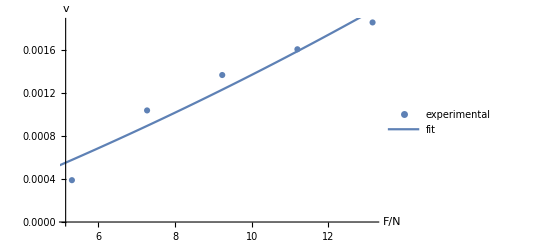

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.00039,0.00104,0.00137,0.00161,0.00186};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

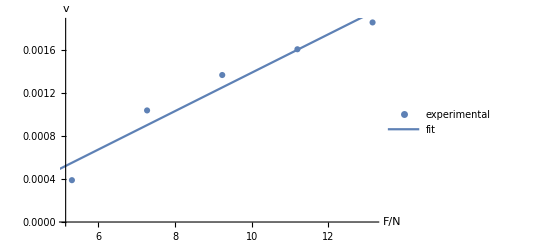

μ_H2O→0.000877757 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.00039,0.00104,0.00137,0.00161,0.00186};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

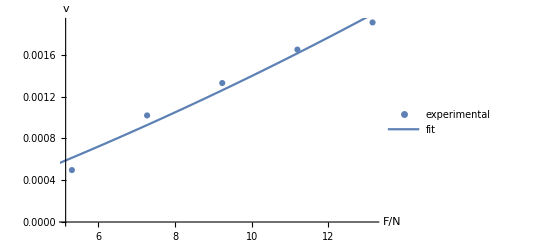

μ_H2O→0.00120907 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000497,0.00102,0.00133,0.00165,0.00191};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

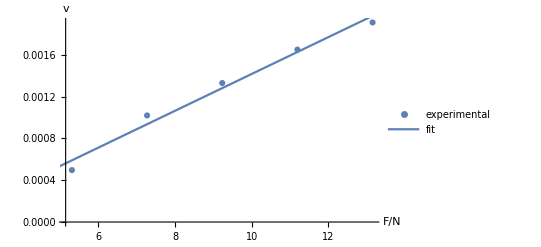

μ_H2O→0.000891471 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000497,0.00102,0.00133,0.00165,0.00191};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

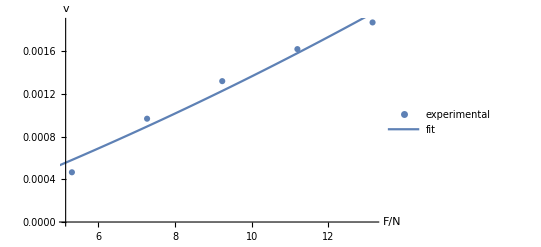

μ_H2O→0.00120809 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000466,0.000968,0.00132,0.00162,0.00187};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

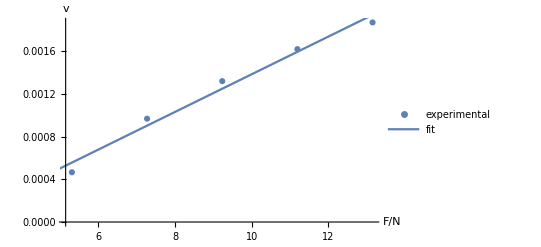

μ_H2O→0.000890441 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000466,0.000968,0.00132,0.00162,0.00187};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

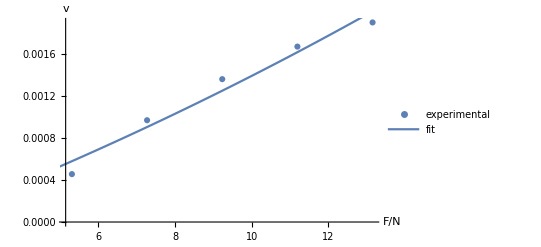

μ_H2O→0.00116535 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000456,0.000969,0.00136,0.00167,0.0019};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

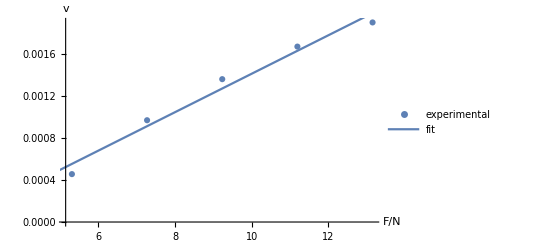

μ_H2O→0.000858436 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000456,0.000969,0.00136,0.00167,0.0019};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

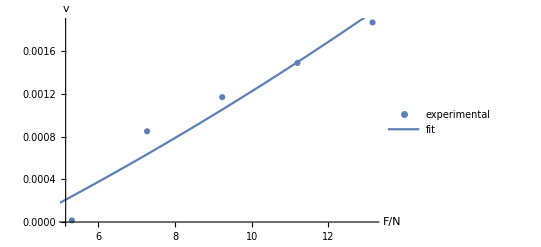

μ_H2O→0.000962267 Pa.s

```mathematica
Clear["Global`*",Subscript]
Subscript[R, 0]=0.0005;Subscript[R, 1]=0.0075;L=5;Subscript[c, 1]=0.00000000038;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000015,0.00085,0.00117,0.00149,0.00187};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 F[[i]]^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 F[[i]]^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 F[[i]]^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 F[[i]]^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 F[[i]])-b)^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"];
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[1/(40 L π^5 μ Subscript[R, 1]^12)(Subscript[c, 1]^4 f^5+20 π Subscript[c, 1]^3  Subscript[R, 0] Subscript[R, 1]^2 f^4+30 π^2 Subscript[c, 1]^2  Subscript[R, 0]^2 Subscript[R, 1]^4 f^3+20 π^3 Subscript[c, 1]  Subscript[R, 0]^3 Subscript[R, 1]^6 f^2+5 π^4  Subscript[R, 0]^4 Subscript[R, 1]^8 f)+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
"μ_H2O"->μ(Pa.s)
```

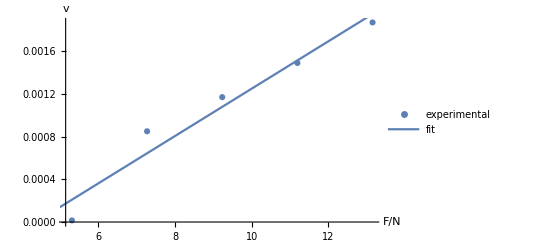

μ_H2O→0.000708259 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.0075;L=5;
F=9.8*Table[0.542+0.2i,{i,0,4}];
Subscript[v, H2O]={0.000015,0.00085,0.00117,0.00149,0.00187};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{fit},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

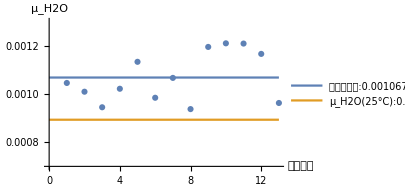

0.00106754

1.04975×10^-8

0.195459

```mathematica
Clear["Global`*",Subscript]
Subscript[μ, H2O]={0.00104506,0.00100891,0.000944548,0.00102114,0.00113259,0.000983891,0.00106604,0.000936967,0.00119416,0.00120907,0.00120809,0.00116535,0.000962267};
Show[ListPlot[Subscript[μ, H2O],ImageSize->300,PlotMarkers->Automatic,AxesLabel->{"实验次数","μ_H2O"},PlotRange->{0.0007,0.0013}],Plot[{Mean@Subscript[μ, H2O],0.000893},{x,0,Length@Subscript[μ, H2O]},PlotLegends->{平均测量值:Mean@Subscript[μ, H2O]Pa.s,"μ_H2O(25°C):0.000893Pa.s"}]]
Mean@Subscript[μ, H2O]
Variance@Subscript[μ, H2O]
Abs[(0.000893-Mean@Subscript[μ, H2O])/0.000893]
```

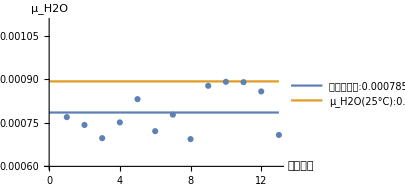

0.000785638

5.64306×10^-9

0.120226

```mathematica
Clear["Global`*",Subscript]
Subscript[μ, H2O]={0.0007698,0.0007427,0.0006973,0.0007516,0.0008318,0.0007214,0.0007783,0.000694,0.0008778,0.0008915,0.0008904,0.0008584,0.0007083};
Show[ListPlot[Subscript[μ, H2O],ImageSize->300,PlotMarkers->Automatic,AxesLabel->{"实验次数","μ_H2O"},PlotRange->{0.0006,0.0011}],Plot[{Mean@Subscript[μ, H2O],0.000893},{x,0,Length@Subscript[μ, H2O]},PlotLegends->{平均测量值:Mean@Subscript[μ, H2O]Pa.s,"μ_H2O(25°C):0.000893Pa.s"}]]
Mean@Subscript[μ, H2O]
Variance@Subscript[μ, H2O]
Abs[(0.000893-Mean@Subscript[μ, H2O])/0.000893]
```

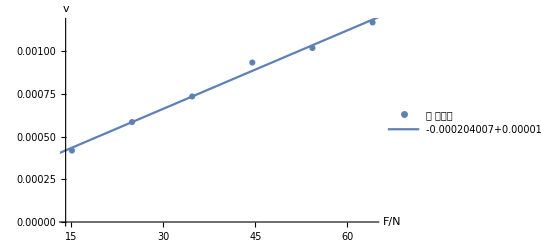

μ_H2O→0.0032457 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[0.542+i,{i,1,6}];
Subscript[v, H2O]={0.000419,0.000586,0.000736,0.000935,0.00102,0.00117};
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

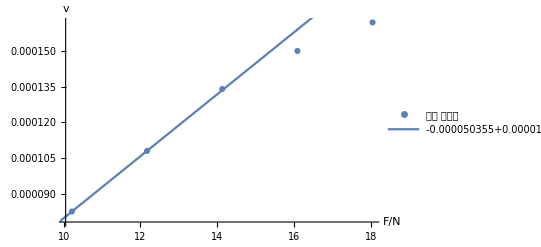

μ_air→0.000238927 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.00025;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[1.042+0.2i,{i,0,4}];
Subscript[v, air]={0.0000825,0.000108,0.000134,0.00015,0.000162};
sol1=NMinimize[Total@Table[(Subscript[v, air][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, air]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{实验值(空气)}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a"F"+b},ImageSize->400]]
"μ_air"->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```

{2.37266×10^-23,{μ→0.000241242,b→-0.0000496955}}

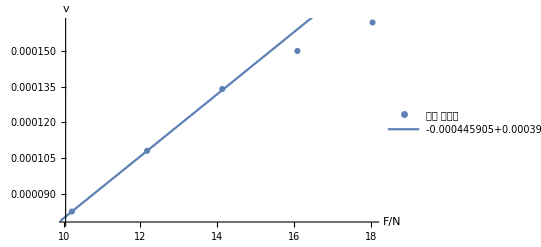

μ_air→0.000241242 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.00025;Subscript[R, 1]=0.01;L=5;k=1.41;Subscript[p, 0]=1.01*10^5;
F=9.8*Table[1.042+0.2i,{i,0,4}];
Subscript[v, air]={0.0000825,0.000108,0.000134,0.00015,0.000162};
sol1=NMinimize[Total@Table[(10^5(Subscript[v, air][[i]]-(k R^4 Subscript[p, 0] ((1+F[[i]]/(π Subscript[p, 0] Subscript[R, 1]^2))^(1/2+3/(4 k))-1))/(2 (3+2 k) L μ Subscript[R, 1]^2)-b))^2,{i,1,Length@Subscript[v, H2O]}],{μ,b},Method->"RandomSearch"]
μ=μ/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, air]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{实验值(空气)}],Plot[(k R^4 Subscript[p, 0] ((1+f/(π Subscript[p, 0] Subscript[R, 1]^2))^(1/2+3/(4 k))-1))/(2 (3+2 k) L μ Subscript[R, 1]^2)+b,{f,0,1.1Max[F]},PlotLegends->{(k R^4 Subscript[p, 0] ((1+("F")/(π Subscript[p, 0] Subscript[R, 1]^2))^(1/2+3/(4 k))-1))/(2 (3+2 k) L μ Subscript[R, 1]^2)+b//Simplify},ImageSize->400]]
"μ_air"->μ(Pa.s)
```

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F=9.8*Table[0.542+i,{i,1,4}];
Subscript[v, H2O]={0.0000353,0.000579,0.000863,0.00129};
Subscript[n, max]=3;
sol1=NMinimize[Total@Table[(Subscript[v, H2O][[i]]-Sum[Subscript[a, n] F[[i]]^n,{n,0,Subscript[n, max]}])^2,{i,1,Length@Subscript[v, H2O]}],Table[Subscript[a, n],{n,0,Subscript[n, max]}],Method->"SimulatedAnnealing"];
Evaluate@Table[Subscript[a, n],{n,0,Subscript[n, max]}]=Table[Subscript[a, n]/.sol1[[2]],{n,0,Subscript[n, max]}];
Show[ListPlot[Transpose@{F,Subscript[v, H2O]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[Sum[Subscript[a, n] F[[i]]^n,{n,0,Subscript[n, max]}],{f,0,1.1Max[F]},PlotLegends->{Sum[Subscript[a, n]("F")^n,{n,0,Subscript[n, max]}]},ImageSize->400]]
Subscript[μ, H2O]->R^4/(8π Subscript[a, 1] Subscript[R, 1]^4 L)(Pa.s)
Table[Subscript[a, n],{n,0,Subscript[n, max]}]
```

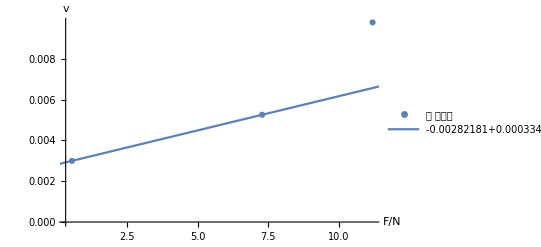

μ_piston→0.000148531 Pa.s

```mathematica
Clear["Global`*",Subscript]
R=0.0005;Subscript[R, 1]=0.01;L=5;
F={0.53214,7.2814,11.2014};
Subscript[v, piston]={0.003,0.00526,0.00979};
sol1=NMinimize[Total@Table[(Subscript[v, piston][[i]]-a F[[i]]-b)^2,{i,1,Length@Subscript[v, H2O]}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
Show[ListPlot[Transpose@{F,Subscript[v, piston]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"F/N","v"},PlotRange->All,PlotLegends->{experimental}],Plot[a f+b,{f,0,1.1Max[F]},PlotLegends->{a "F"+b},ImageSize->400]]
Subscript[μ, piston]->R^4/(8π a Subscript[R, 1]^4 L)(Pa.s)
```